# (2) Behavior

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dir ="../cSrc/";
(*dir = "../AnalysisData/best_offset/";*)
```

## Task 1: Object Recognition

```mathematica
ba=Import[ StringJoin[dir,"B_avoid_aposx.dat"]];
bc=Import[ StringJoin[dir,"B_approach_aposx.dat"]];
aa=Import[ StringJoin[dir,"A_avoid_aposx.dat"]];
ac=Import[ StringJoin[dir,"A_approach_aposx.dat"]];
```

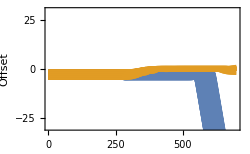

```mathematica
Show[{ListLinePlot[ba,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[bc,PlotRange->All,PlotStyle->cd[[2]]]},PlotRange->{Automatic,{-30,30}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
(*Export["BehaviorB.eps",%]*)
```

## Task 2: Perceiving Affordances

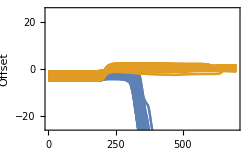

```mathematica
Show[{ListLinePlot[aa,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[ac,PlotRange->All,PlotStyle->cd[[2]]]},PlotRange->{Automatic,{-25,25}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
(*Export["BehaviorA.eps",%]*)
```

## Both tasks

```mathematica
Show[{ListLinePlot[ba,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[bc,PlotRange->All,PlotStyle->cd[[2]]],ListLinePlot[aa,PlotRange->All,PlotStyle->cd[[3]]],ListLinePlot[ac,PlotRange->All,PlotStyle->cd[[4]]]},PlotRange->{Automatic,{-25,25}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
(*Export["BehaviorC.eps",%]*)
```

-Graphics-